## Set up

```mathematica
alpha=2;
l=13;
hd="";
fl="";
wd=StringJoin[hd,fl];
SetDirectory[wd];
```

```mathematica
nrep=3;
nprop=13;
schemes={"random","noised","mut"};
nschemes=Length@schemes;
```

```mathematica
A=Range[0,alpha-1];(*the alphabet in numbers 0-19*)
sequences=Tuples[A,l];(*list of all sequences*)
seq2pos[seq_]:=FromDigits[seq,alpha]+1;
multiplicities=Table[Binomial[l,k](alpha-1)^k,{k,0,l}]; 
wt=ConstantArray[0,l];
AA={"A","C","G","T"};
AAtoDigitRules = {"A"->0,"C"->1,"G"->2,"T"->3};
DigitToAARules = {0->"A",1->"C",2->"G",3->"T"};
sequencesAA=StringJoin[#/.DigitToAARules]&/@sequences;
wtAA = sequencesAA[[1]];
mks=Table[Binomial[l,k](alpha-1)^k, {k,0,l}];
```

```mathematica
MakeLapRec[alpha_,l_]:=Module[{L1,L,m},
L1 = SparseArray[alpha*IdentityMatrix[alpha] - ArrayReshape[ConstantArray[1,alpha^2],{alpha,alpha}]];
m=1;
L=L1;
While[m<l, L = KroneckerProduct[L, IdentityMatrix[alpha]] + KroneckerProduct[IdentityMatrix[alpha^m],L1];
m++];
L
]
L=MakeLapRec[alpha,l];//AbsoluteTiming
```

{0.078818,Null}

```mathematica
samplesizes=Table[Round[i Length[sequences]],{i,Join[{.01,.05},Range[.1,.9,.1],{.95,.99}]}];
proportions=samplesizes/(alpha^l);
```

## *Functions

### Basic functions

```mathematica
dp[v_]:=v//DeleteDuplicates
uqc[v_]:=v//DeleteDuplicates//Length
lg[v_]:=v//Length
dim[m_]:=m//Dimensions
```

```mathematica
seq2posAA[seqAA_]:=seq2pos[Characters[seqAA]/.AAtoDigitRules]
```

```mathematica
associate0[list_,obj_]:=Table[list[[i]]->obj,{i,Length[list]}]
```

```mathematica
MakeDiagonal[vect_]:= SparseArray[Table[{i,i}->vect[[i]],{i,Length[vect]}]]
```

```mathematica
Nbysum[y_]:=(1/Total[y])*y
Nbyfirst[y_]:=(1/First@y)*y
```

```mathematica
ginv[x_]:=If[N[x]==0.,0,1/x]
```

```mathematica
r2[x_, y_] := If[Length@x<2, {}, Correlation[x, y]^2];


mse[x_, y_] := Mean[(x - y)^2];
maxorder[list_] := 
  Module[{i}, 
   For[i = 1, list[[i ;;]] != ConstantArray[0, Length[list[[i ;;]]]], 
    i++]; i - 1];

(*From sequence to lexicographical position*)

seq2pos[seq_] := FromDigits[seq, alpha] + 1

(*Map a vector of length m to a vector of length alpha^l. "list" contains the lexicographical positions for all sequences in "data"*)MapPartialVal[list_,data_,height_]:=Module[{Ab},Ab=SparseArray[Transpose[{list,Range[1,Length[list]]}]->1,{height,Length[list]}];Ab.data]
```

```mathematica
(*Krawtchouk polynomial*)
w[alpha_, k_, d_] := alpha^(-l) ∑_(q=0)^Min[k,d] (-1)^q(alpha-1)^(k-q)Binomial[d,q]Binomial[l-d,k-q]
wkd = Table[w[alpha,k,d],{d,0,l},{k,0,l}];
```

### Matrix coefficients

```mathematica
(*LPs contains entries of L^n defined at d=0,1,...l. For any matrix whose (i,j)-th entry only depends on d(i,j), we can then solve a linear equation for the coefficients*)
B=SparseArray[{i_,i_}->(alpha-1)*l,{l+1,l+1}]-1*(SparseArray[{i_,j_}/;i==j:>(i-1)*(alpha-2),{l+1,l+1}]+SparseArray[{i_,j_}/;i-j==1:>i-1,{l+1,l+1}]+SparseArray[{i_,j_}/;i-j==-1:>(l-j+2)*(alpha-1),{l+1,l+1}]);
LPs=ArrayReshape[{PadRight[{1},l+1],PadRight[{(alpha-1)*l,-1},l+1],Table[MatrixPower[B,i].PadRight[{(alpha-1)*l,-1},l+1],{i,1,l-1}]},{l+1,l+1}]//Transpose;
```

### Projection operators

```mathematica
Pby[x_,Pcoeffs_]:=Pcoeffs[[1;;maxorder[Pcoeffs]]].NestList[L.#&,x,maxorder[Pcoeffs]-1];
```

```mathematica
Pkby[x_,k_]:=Module[{Pcoeffs},Pcoeffs=Inverse[LPs].wkd[[All,k+1]];Pcoeffs[[1;;maxorder[Pcoeffs]]].NestList[L.#&,x,maxorder[Pcoeffs]-1]];
```

## Generate simulated landscape

```mathematica
lambdas=Nbyfirst@Table[2^(l-i) (1 + (alpha-1)*.5)^(l-i),{i,1,l}];
```

```mathematica
VCExpected=Nbysum[Rest@mks*lambdas]//N;
```

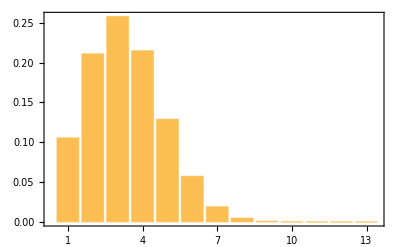

```mathematica
BarChart[VCExpected, Frame->True, FrameTicks->{{Automatic,None},{Transpose[{Range@l,Range@l}],None}}]
```

```mathematica
phi=RandomVariate[NormalDistribution[],alpha^l];phi=Table[Sqrt[(lambdas[[k]]mks[[k+1]]/Norm[Pkby[phi,k]]^2)]Pkby[phi,k],{k,1,l}]//Total;
phi = phi/StandardDeviation[phi];
y = LogisticSigmoid[phi];
```

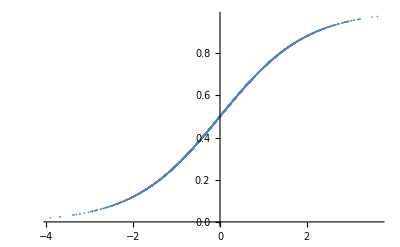

```mathematica
ListPlot[Transpose@{phi, y}, PlotRange->All]
```

```mathematica
VCObs = Table[Norm[Pkby[y,k]]^2, {k, 1, l}];
VCObs = VCObs/Total@VCObs;
Export["VCobs.csv", VCObs];
```

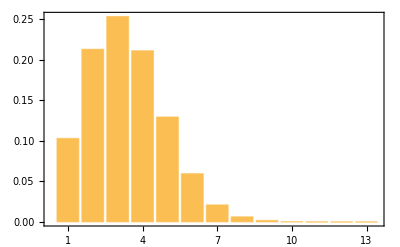

```mathematica
BarChart[VCObs, Frame->True, FrameTicks->{{Automatic,None},{Transpose[{Range@l,Range@l}],None}}]
```

```mathematica
Export["phi.tsv", Transpose@{sequencesAA, phi}];
Export["y.tsv", Transpose@{sequencesAA, y}];
```

## Calculate variance components for epistatic transformer predictions with 1, 2, 3 MHA layers

```mathematica
preds = Table[Import[StringJoin["pred_", i, ".csv"]][[2;;, 2;;]]//Flatten, {i, {"1_layer", "2_layers", "3_layers"}}];
```

```mathematica
VCPreds = Table[Table[Norm[Pkby[preds[[i]],k]]^2, {k, 1, 8}], {i, 3}];
```

```mathematica
VCPreds
```

{{819.227,1717.13,4.24662×10^-12,8.31694×10^-12,1.28413×10^-11,1.76225×10^-11,1.7757×10^-11,1.28332×10^-11},{877.656,1708.72,2127.1,1752.37,7.22975×10^-11,9.33883×10^-11,9.32209×10^-11,6.58253×10^-11},{857.063,1710.33,2109.83,1708.54,1016.94,436.848,119.403,8.67677}}

```mathematica
Do[VCPreds[[i]] = VCPreds[[i]]/Total@VCPreds[[i]], {i, 3}];
```

```mathematica
Export["VC_predictions.csv", VCPreds];
```

## Calculate variance components for 3-layer epistatic transformer at different epochs

```mathematica
epochs = Range[0, 3900, 100];
```

```mathematica
epochs
```

{0,100,200,300,400,500,600,700,800,900,1000,1100,1200,1300,1400,1500,1600,1700,1800,1900,2000,2100,2200,2300,2400,2500,2600,2700,2800,2900,3000,3100,3200,3300,3400,3500,3600,3700,3800,3900}

```mathematica
predsEpochs=Table[{},Length[epochs]];
VCEpochs=Table[{},Length[epochs]];
```

```mathematica
Do[
predsEpochs[[i]] = Import[StringJoin["preds_epochs/pred_epoch", ToString[epochs[[i]]], ".csv"] ][[2;;, 2;;]]//Flatten, {i, Length@epochs}]
```

```mathematica
Do[
VC = Table[Norm[Pkby[predsEpochs[[i]],k]]^2, {k, 1, 8}];
VC = VC/Total@VC;
VCEpochs[[i]] = VC,
{i, Length@epochs}
]
```

```mathematica
VCEpochs//Dimensions
```

{40,8}

```mathematica
Export["VCEpochs.csv", VCEpochs];
```